## T[1][2] (T_μτ) : Plots_Near χ^2(var) - One variable only

#### 2_Reducing a list of 2 variables to 1 : { Var, Var2, χ^2 } → { Var, χ^2 }

```mathematica
Red2for1[Inlist_, Var_, Var2_]:=
Module[{tab,lis,nunN,nun3,newlisOne,list,nun,nun2,newlis,NewlisOne},
(* Código da função *)
list=Inlist;

(* Creating the list: { Var, χ^2 } *)
nun={};nun2={};
tab=Table[{list[[i,Var]],list[[i,Var2]],list[[i,3]]},{i,Length@list}];
lis=tab[[Ordering@PadRight@tab]]; 
If[Var==1,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
,
Do[
	If[ Length[nun]== 0,If[lis[[1,Var2]]≠ lis[[i,Var2]],AppendTo[nun,i]] ]
,{i,Length@lis}];
Do[
	If[ Length[nun2]== 0,If[lis[[1,Var]]≠ lis[[i,Var]],AppendTo[nun2,i]] ]
,{i,Length@lis}];
];
nunN=(nun-{1})/(nun2-{1});
nun2=nun2-{1};
nun3=(Length@lis)/(nunN*nun2);

newlisOne=Table[
{
 lis[[1+i*nunN[[1]],1]],
Min[ lis[[1+i*nunN[[1]]*nun2[[1]];;(1+i)*nunN[[1]],3]] ]
 }
,{i,0,nun3[[1]]-1}];


(* Return: *)
NewlisOne=newlisOne
]
```

#### 3_Type - 1a : ϵ_μτ

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_03_Near_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];

text = "DUNE_Near_NSI_fit2D_eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list, 1, 2];
newlis

textBG = "DUNE_Near_NSI_fit2D_BG_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG, 1, 2];
newlisBG
```

{{-0.0001,42.7731},{-0.00009,34.0334},{-0.00008,26.2723},{-0.00007,19.4966},{-0.00006,13.7148},{-0.00005,8.93852},{-0.00004,5.18257},{-0.00003,2.46355},{-0.00002,0.787115},{-0.00001,0.0850223},{0.,0.},{0.00001,0.0833236},{0.00002,0.78017},{0.00003,2.45037},{0.00004,5.1631},{0.00005,8.91286},{0.00006,13.6831},{0.00007,19.4589},{0.00008,26.2287},{0.00009,33.9838},{0.0001,42.7177}}

{{-0.0001,7.73084},{-0.00009,5.44165},{-0.00008,3.70612},{-0.00007,2.45443},{-0.00006,1.61038},{-0.00005,0.8975},{-0.00004,0.442086},{-0.00003,0.183086},{-0.00002,0.0552158},{-0.00001,0.00681553},{0.,0.},{0.00001,0.00672439},{0.00002,0.0548278},{0.00003,0.182117},{0.00004,0.440144},{0.00005,0.894121},{0.00006,1.60635},{0.00007,2.44802},{0.00008,3.69682},{0.00009,5.42894},{0.0001,7.71428}}

##### Without_BG

0.

{{11}}

0.

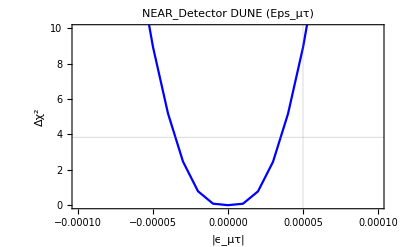

```mathematica
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* Without BG *)
plot=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["without_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.00005},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"NEAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### With_BG

0.

{{11}}

0.

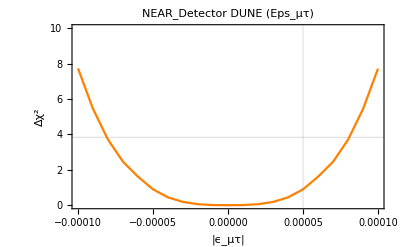

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.00005},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"NEAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

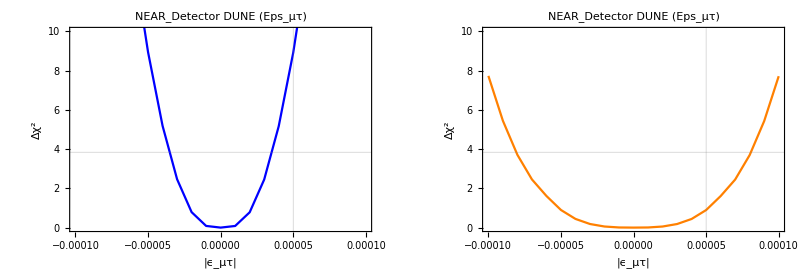

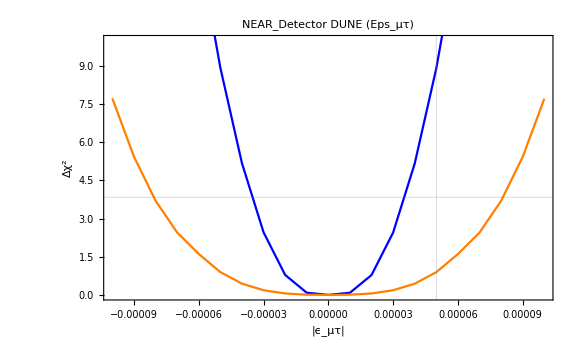

```mathematica
GraphicsRow[{plot,plotBG}]
Show[plot,plotBG,ImageSize->Large]
```

#### 3_Type - 1b : α

```mathematica
(*pathImpor="/home/edson/Projeto_doutorado/Experimentos/Beam_Tau/DUNE_py/NSI_03_Near_DUNE/my_data_2D/";*)
pathImpor=NotebookDirectory[];
text = "DUNE_Near_NSI_fit2D_eps_alpha";
list=Import[StringJoin[pathImpor,text]];
newlis=Red2for1[list,2, 1];
newlis

textBG = "DUNE_Near_NSI_fit2D_BG_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG,2, 1];
newlisBG
```

{{-0.5,20.},{-0.45,16.2},{-0.4,12.8},{-0.35,9.8},{-0.3,7.2},{-0.25,5.},{-0.2,3.2},{-0.15,1.8},{-0.1,0.8},{-0.05,0.2},{0.,0.},{0.05,0.2},{0.1,0.8},{0.15,1.8},{0.2,3.2},{0.25,5.},{0.3,7.2},{0.35,9.8},{0.4,12.8},{0.45,16.2},{0.5,20.}}

{{-0.5,79.5485},{-0.45,61.8339},{-0.4,47.2757},{-0.35,35.2926},{-0.3,25.3733},{-0.25,17.3082},{-0.2,10.9275},{-0.15,6.09637},{-0.1,2.71415},{-0.05,0.698439},{0.,0.},{0.05,0.703184},{0.1,2.75074},{0.15,6.05891},{0.2,10.5546},{0.25,16.1738},{0.3,22.8597},{0.35,30.5621},{0.4,39.2364},{0.45,48.8425},{0.5,59.3443}}

##### Without_BG

0.

{{11}}

0.

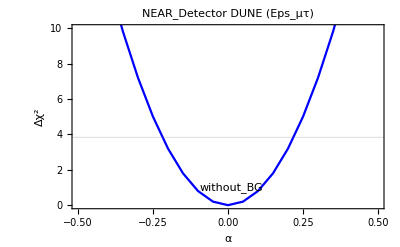

```mathematica
data = newlis;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Blue];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* Without BG *)
plot=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["without_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"NEAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### With_BG

0.

{{11}}

0.

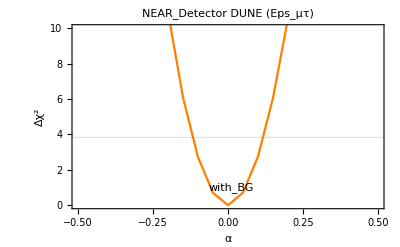

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"NEAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

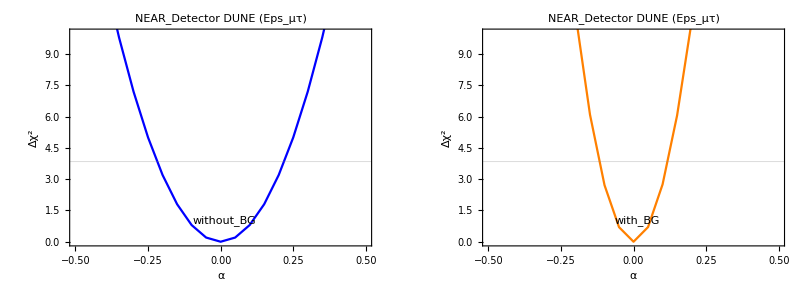

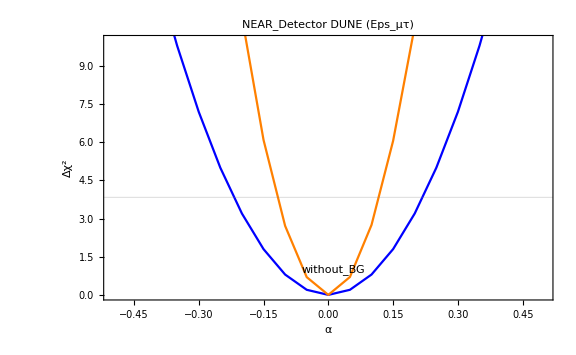

```mathematica
GraphicsRow[{plot,plotBG}]
Show[plot,plotBG,ImageSize->Large]
```

#### 3_Type - 2a : ϵ_μτ

```mathematica
pathImpor=NotebookDirectory[];

textBG = "DUNE_Near_NSI_fit2D_BG2_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG, 1, 2];
newlisBG
```

{{-0.0001,7.73084},{-0.000095,6.51295},{-0.00009,5.44165},{-0.000085,4.50888},{-0.00008,3.70612},{-0.000075,3.02443},{-0.00007,2.39878},{-0.000065,1.87172},{-0.00006,1.4387},{-0.000055,1.08984},{-0.00005,0.815195},{-0.000045,0.604843},{-0.00004,0.442086},{-0.000035,0.292367},{-0.00003,0.183086},{-0.000025,0.106372},{-0.00002,0.0552158},{-0.000015,0.023644},{-0.00001,0.00681553},{-5.×10^-6,0.000647133},{0.,0.},{5.×10^-6,0.000628651},{0.00001,0.00672439},{0.000015,0.0234325},{0.00002,0.0548278},{0.000025,0.105737},{0.00003,0.182117},{0.000035,0.290966},{0.00004,0.440144},{0.000045,0.602777},{0.00005,0.812386},{0.000055,1.08616},{0.00006,1.43401},{0.000065,1.86589},{0.00007,2.39168},{0.000075,3.01664},{0.00008,3.69682},{0.000085,4.49793},{0.00009,5.42894},{0.000095,6.49837},{0.0001,7.71428}}

##### With_BG

0.

{{21}}

0.

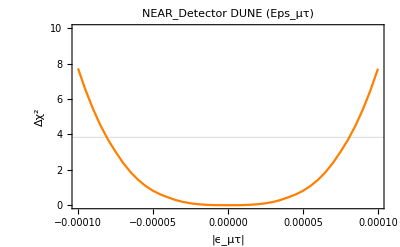

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["|ϵ_μτ|",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{0.006},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"NEAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

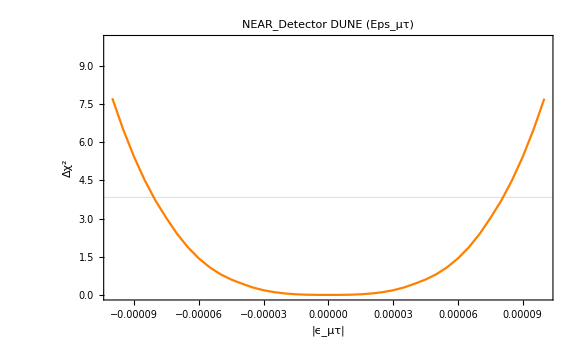

```mathematica
Show[plotBG,ImageSize->Large]
```

#### 3_Type - 2b : α

```mathematica
pathImpor=NotebookDirectory[];

textBG = "DUNE_Near_NSI_fit2D_BG2_eps_alpha";
listBG=Import[StringJoin[pathImpor,textBG]];
newlisBG=Red2for1[listBG,2, 1];
newlisBG
```

{{-0.5,79.5485},{-0.475,70.2663},{-0.45,61.8339},{-0.425,54.1883},{-0.4,47.2757},{-0.375,41.0114},{-0.35,35.2926},{-0.325,30.0828},{-0.3,25.3529},{-0.275,21.091},{-0.25,17.2745},{-0.225,13.883},{-0.2,10.8982},{-0.175,8.30368},{-0.15,6.08507},{-0.125,4.22915},{-0.1,2.71415},{-0.075,1.54389},{-0.05,0.697926},{-0.025,0.177265},{0.,0.},{0.025,0.177839},{0.05,0.703184},{0.075,1.56442},{0.1,2.75074},{0.125,4.25204},{0.15,6.05891},{0.175,8.16253},{0.2,10.5546},{0.225,13.2275},{0.25,16.1738},{0.275,19.3866},{0.3,22.8597},{0.325,26.5867},{0.35,30.5621},{0.375,34.7804},{0.4,39.2364},{0.425,43.9253},{0.45,48.8425},{0.475,53.9835},{0.5,59.3443}}

##### With_BG

0.

{{21}}

0.

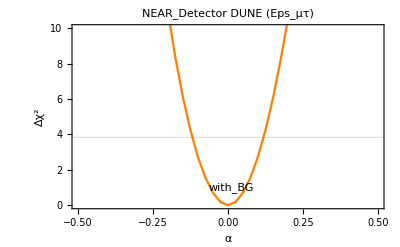

```mathematica
data = newlisBG;
x=Transpose[data][[1]];
chi2= Transpose[data][[2]];

min=Min[chi2]
pos = Position[chi2,min]
xmin=x[[pos[[1,1]]]]

(* Data_Plot *)
DataMin=Table[{x[[i]],chi2[[i]]-min},{i,1,Length[x]}];
PlotChi2NO=ListPlot[DataMin, Joined->True, PlotStyle->Orange];


(* Label *)
label=
Grid[
{
{Graphics[{Thick,RGBColor[0,0.68,0.63],Line[{{0.1,0.1},{1,0.1}}]},ImageSize->20],Style["NOνA",16]}
},
Alignment->Center,Background->None];


(* With BG *)
plotBG=
Show[{PlotChi2NO},
Frame-> True,
FrameLabel-> { Style["α",FontSize-> 22] , Style["Δχ^2",FontSize-> 22] },
Epilog-> {
	Style[Text["with_BG",{0.012,1}],15,FontFamily-> "DejaVu Serif"]
	},
FrameStyle->Directive[Black,Thick,FontSize-> 14,FontFamily-> "DejaVu Serif"], 
LabelStyle-> Black,
GridLines->{{},{3.84}},

PlotRange->{{Min[x],Max[x]},{0,10}},
PlotLabel->"NEAR_Detector DUNE (Eps_μτ)",
PlotRangePadding-> None]
```

##### Both

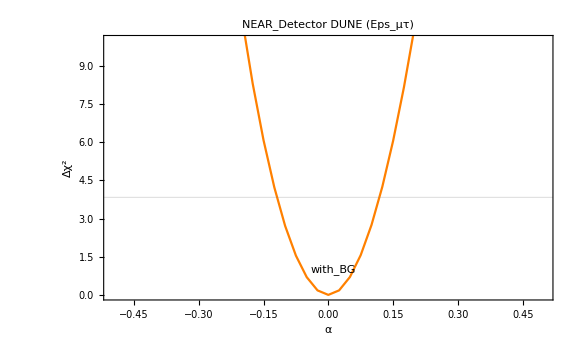

```mathematica
Show[plotBG,ImageSize->Large]
```